## Coursework 1

The following two subsections contain the examples from the initial coursework assignment sheet. The solved exercises are listed below.

# Example using Plot function

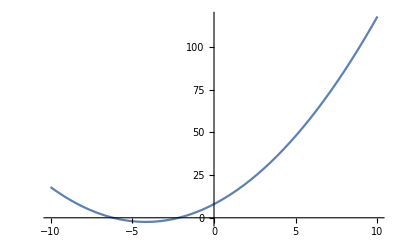

```mathematica
Plot[0.6 x^2 + 5 x + 8, {x, -10, 10}]
```

### Anti-crossing in quantum mechanics

```mathematica
symmetric2x2={{e0,v}, {v, e1}};
```

```mathematica
symmetric2x2//MatrixForm
```

(e0 | v
v | e1)

```mathematica
ham = symmetric2x2 /.{e0->x, e1->1,v->1/10};
```

```mathematica
ham // MatrixForm
```

(x | 1/10
1/10 | 1)

```mathematica
evals=Eigenvalues[ham]
```

{1/10 (5+5 x-√(26-50 x+25 x^2)),1/10 (5+5 x+√(26-50 x+25 x^2))}

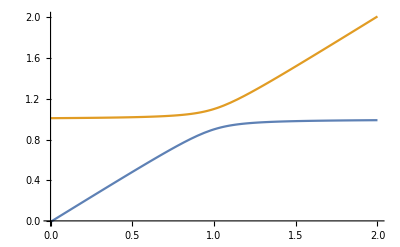

```mathematica
Plot[evals,{x,0,2}]
```

### Exercise 1: Basis state mixing

-Graphics-

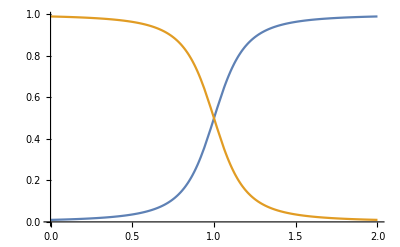

```mathematica
rules={e0->x, e1->1, v->10/100};
ham=symmetric2x2/.rules;
evals=Eigenvalues[ham];
Plot[evals,{x,0,2}]
evecs:=Eigenvectors[ham];
prob1:=Abs[Transpose[evecs][[1]]]^2;
Plot[prob1,{x,0,2}]
```

Namingconvention:Ĥ=(e_0 | V
V | e_1)=(x | 1/10
1/10 | 1),|Ψ_0>=( 1 
 0 )|Ψ_1>=( 0 
 1 ),  Ψ_±>==E_±|Ψ_±>

The configured Hamiltonian describes the behaviour of two energy states ( and )  that are coupled over a 
fixed interaction potential (). The lower initial energy state is changed linearly with a parameter x.

The upper graph shows the evolution of the energies of the new eigenstates  and   as function of x, 
here now referred as   and . For  it is  and  which is the initial state without an interaction.
Until about x=0.8  rises linearly with x and  remains roughly constant which corresponds to the behaviour of the 
initial energies without an interaction. For x>0.8 the interaction becomes relevant. The linear behavior of  transitions 
into constant behaviour while  changes from constant to linear behaviour with f(x)=x as asymptote.

The lower graph shows the probability of measuring the initial eigenstate  in the resulting eigenstates
 (red line) and (blue line). For x=0  is almost 1 and stays close to 1 for 
 which means that the interaction has only small influence on the final eigenstates for small x. This agrees also with 
 the energy plot where the eigenstates only differed from the initial energies for x>0.8. For x around 1,  drops significantly
 with a linear phase at x=1. Its slope becomes shallower while approaching . Both probabilities are point symmetric
 in (1, 0.5) and add up to 1. This shows, that the state with increasing energy  first mainly contributes to , then 
 mixes with  and finally mainly contributes to the higher energy state . This can be also seen in the energy plot.

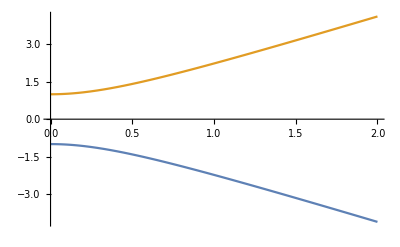

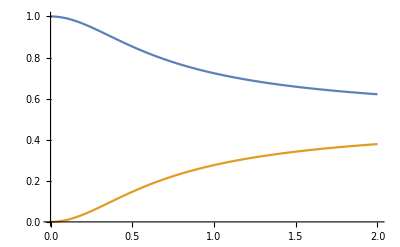

```mathematica
rules0={e0->-1, e1->1, v->2x};
ham=symmetric2x2/.rules0;
evals=Eigenvalues[ham];
Plot[evals,{x,0,2}]
evecs:=Eigenvectors[ham];
prob1:=Abs[Transpose[evecs][[1]]]^2;
Plot[prob1,{x,0,2}]
```

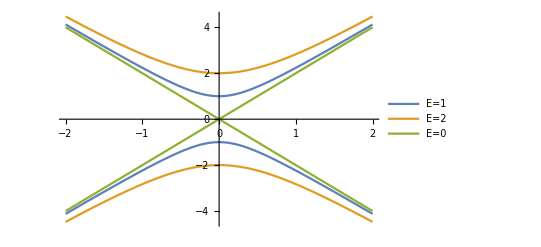

```mathematica
rules1 ={e0->-2, e1->2, v->2x};
rules2={e0->0, e1->0, v->2x};
Plot[{Eigenvalues[symmetric2x2/. rules0],Eigenvalues[symmetric2x2/. rules1],Eigenvalues[symmetric2x2/. rules2]},{x,-2,2}, PlotLegends->{"E=1", "E=2", "E=0"}]
```

### Exercise 2: Spin-spin interactions

```mathematica
echarge=1.602 10^-19(*in C*);
```

```mathematica
emass=9.11 10^-31(*in kg*);
```

```mathematica
hbar=1.05 10^-34(*in Js*);
```

```mathematica
bohrmagneton=hbar/(2 emass) 10^6 (*in µeV/T*)
```

57.629

```mathematica
r=2.793 emass/(1.673 10^-27)
```

0.00152087

```mathematica
Ehfs=5.87433 ;(*in µeV*)
B0=Ehfs / bohrmagneton (* in T*)
```

0.101934

```mathematica
H={{1/4-, 0, 0, 0},{0, -1/4-, 1/2, 0},{0, 1/2, -1/4+, 0},{0,0,0,1/4+}};
H//MatrixForm (*Hamiltonian without Ehfs factor*)
```

(1/4-x_- | 0 | 0 | 0
0 | -1/4-x_+ | 1/2 | 0
0 | 1/2 | -1/4+x_+ | 0
0 | 0 | 0 | 1/4+x_-)

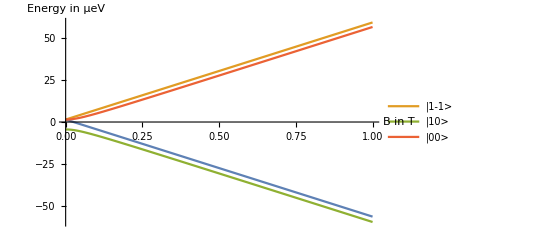

{{1.,0,0,0},{0,0,0,1.},{0,1.,1.,0},{0,-1.,1.,0}}

```mathematica
Heval=Ehfs H/.{->(1+r)B/B0, ->(1-r)B/B0};
energies=Eigenvalues[Heval];
Plot[energies,{B,0,1}, AxesLabel->{"B in T", "Energy in µeV"}, PlotLegends->{"","|1-1>","|10>","|00>"}]
evecs/.{B->0}
```

Labelling of the lines is based on the resulting eigenvector basis

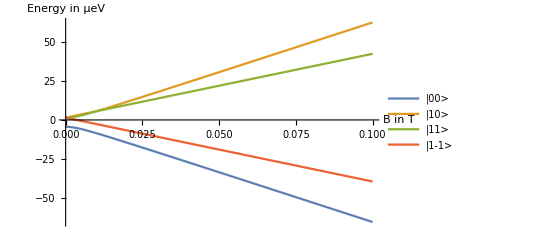

{-409.152,412.089,-642.612,639.675}

```mathematica
B1=B0 0.5;
r2=r;
Heval=Ehfs H/.{->(1+r2)B/B1, ->(1-r2)B/B1};
energies:=Eigenvalues[Heval]
Plot[energies,{B,0,0.1}, AxesLabel->{"B in T", "Energy in µeV"}, PlotLegends->{"|00>", "|10>","|11>","|1-1>"}]
energies/.{B->1}
```

Proof for myself that evecs[4] is has the lowest energy:

```mathematica
evecs:=Eigenvectors[Heval]/.{B->0}
groundstate= evecs[[4]] / Sqrt[Sum[evecs[[4]][[i]]^2,{i,1,4}]];
Heval.groundstate/.{B->0}//MatrixForm
groundstate
```

(0.
3.11533
-3.11533
0.)

{0.,-0.707107,0.707107,0.}

Altering B0 changes the scale of the x-axis, meaning that the slope of the functions becomes steeper with increasing it and vice versa.
Increasing r also leads to steeper slopes of the eigenenergies but affects the states |10> and |00> much more than |11> and |1-1>. For

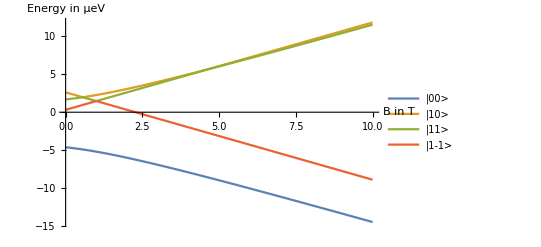

```mathematica
Heval=Ehfs H/.{->(1+x)B/B1, ->(1-x)B/B1}/.{B->0.01};
energies:=Eigenvalues[Heval]
Plot[energies,{x,1/1000,10}, AxesLabel->{"B in T", "Energy in µeV"}, PlotLegends->{"|00>", "|10>","|11>","|1-1>"}]
```

### Exercise 3: The Dirac Equation

```mathematica
antidiagonal=RotateRight[IdentityMatrix[2],1];
σx=antidiagonal;
σy=RotateRight[DiagonalMatrix[{-I,I}],{0,1}];
σz=DiagonalMatrix[{1,-1}];
αx=KroneckerProduct[antidiagonal,σx];
αy =KroneckerProduct[antidiagonal,σy];
αz=KroneckerProduct[antidiagonal,σz];
β=DiagonalMatrix[{1,1,-1,-1}];
```

```mathematica
Hdirac=αx kx+αy ky +αz kz+β m ;
Hdirac//MatrixForm
```

(m | 0 | kz | kx-ⅈ ky
0 | m | kx+ⅈ ky | -kz
kz | kx-ⅈ ky | -m | 0
kx+ⅈ ky | -kz | 0 | -m)

viii) Energy plot

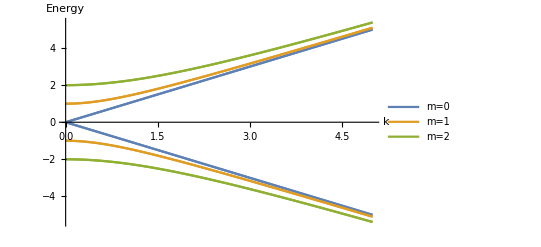

```mathematica
Heval=Hdirac/.{kz->k, kx->0, ky->0 };
evalseq=Table[Eigenvalues[Heval/.{m->i}],{i,0,2}];
Plot[evalseq,{k,0,5},AxesLabel->{"k","Energy"}, PlotLegends->{"m=0","m=1","m=2"} ]
```

ix) The energy curves can be explained over the relativistic energy-impulse relation E^2=m0^2+p^2 (natural units). Rearranging
for E gives E=sqrt(m0^2+p^2) = sqrt(m0^2+k^2). This explains why particles with mass m=0 (e.g photons) have a linear dispersion
with slope dE/dk=1=c/hbar as represented by the blue line and particles with mass m>0 approach this linear relation
asymptotically for large k. In the case of very high energies m0/p becomes negligible and the dispersion relation becomes linear.

x)

```mathematica
U=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
Udagger=ConjugateTranspose[U];
Udagger.U//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
newH = Udagger.Heval.U;
newH//MatrixForm
```

(m | k | 0 | 0
k | -m | 0 | 0
0 | 0 | m | -k
0 | 0 | -k | -m)

The Hamiltonian is now in block diagonal form with 2x2 matrices of the same form as symmetric2x2 which was investigated in exercise 1. For each spin state it is e0=m, e1=-m and v=k in terms of the previous variables. This means that the lower plot shown in fig.1 from the problem sheet represents the probabilites of